```mathematica
aa={{Subscript[X, 8,1],Subscript[X, 1,7],0,0,0,0},{0,Subscript[X, 2,1],0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}};
bb={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
cc={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}};
dd={{0,0},{0,0},{0,0},{0,0}};
```

```mathematica
a=aa/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
b=bb/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
c=cc/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
d=dd/.MapThread[Rule,{Variables[Join[aa,bb,cc,dd]],Map[Subscript[Z, #]&,Range[Length[Variables[Join[aa,bb,cc,dd]]]]]}];
```

```mathematica
jakemoduliGauging2[a,b,c,d];
```

```mathematica
P
```

{{1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,1,1,0,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,0},{0,1,1,0,0,0,1,0,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,1,1,1,1,0,0,1,0,1,1},{0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1},{0,0,1,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1},{0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,1,1,1,1,0,0,0,0,0,1,1,0,1,0,0},{0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0,1,1,0,1,0,1,1,0,1,0,0,0,0,0,1,0},{1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0}}

```mathematica
Gmoduli
```

{{1,1,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,1,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,0,0,0,0},{1,1,1,0,0,1,0,1,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,0,0,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,0},{0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,0,1,1,0,0,1,1,0,0,1,1,0,0,0,0,1,1,1,0,0,1,1,1,0,0,0,1,0,0},{0,1,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,0,1,0,0,1,0,1,1,1,1,1,0,1},{0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0}}

```mathematica
reducibility[P,Gmoduli]
```

True

```mathematica
BFTdim[P]
```

9

```mathematica
reduction[P,Gmoduli,1]
```

Level is 1 and we have to check 20 guys.

Level is 2 and we have to check 1 guys.

Can remove 1 legs in 2 different ways.

Sets of legs that can be Higgsed are 'higgslist'= {{Z_6},{Z_19}}

```mathematica
higgs[Subscript[Z, 6],Xlist,P,Gmoduli]
```

After killing Z_6 the Master space has dimension 8 and the moduli space has dimension 5 .

The new P matrix is saved under 'Phiggs'. New moduli space under 'Gmodulihiggs'. New Xlist under 'Xlisthiggs'.

```mathematica
reducibility[Phiggs,Gmodulihiggs]
```

False

```mathematica
BFTdim[Phiggs]
```

8

```mathematica
PlanarGraphQ[-Graphics-]
```

True

```mathematica
<<GraphUtilities`
```

VertexList::graph: A graph object is expected at position 1 in VertexList[{}].

VertexList::graph: A graph object is expected at position 1 in VertexList[1].

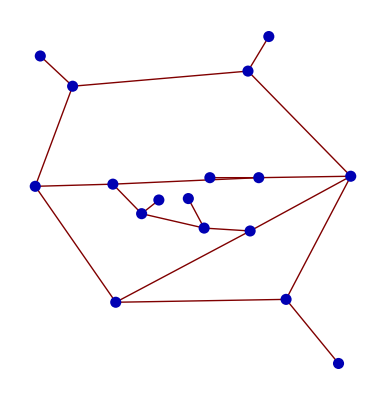
{-Graphics-,Graph→{1→2,1→3,2→4,1→5,5→6,6→7,7→8,8→2,7→9,5→10,6→11,11→8,8→12,12→13,12→10,11→14,14→15,15→10,15→16,14→17},Coordinates→{{122,681},{366,702},{77,723},{395,750},{70,542},{182,381},{419,385},{509,556},{492,296},{178,545},{369,480},{381,554},{313,554},{305,484},{218,504},{242,523},{283,525}},VertexLabels→{1,2,3,3,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}}

```mathematica
GraphEdit[]
```

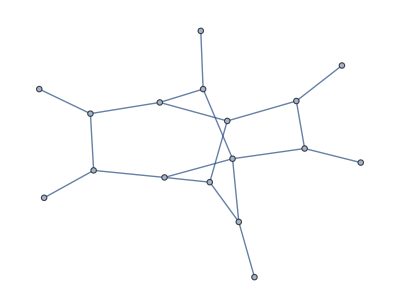

```mathematica
UndirectedGraph[Graph[{1->2,1->3,2->4,1->5,5->6,6->7,7->8,8->2,7->9,5->10,6->11,11->8,8->12,12->13,12->10,11->14,14->15,15->10,15->16,14->17}]]
```

```mathematica
hahas=RandomGraph[{100,90},10];
For[gi=1,gi<Length[hahas]+1,gi++,
Print[AbsoluteTiming[PlanarGraphQ[hahas[[gi]]]]];
];
```

{0.000136843,True}

{0.000197852,False}

{0.000197282,False}

{0.000154518,False}

{0.000151668,False}

{0.000150527,False}

{0.000184738,True}

{0.000182457,False}

{0.000149957,True}

{0.000140834,False}

```mathematica
9!Mean[{0.00013684289751151192,0.00019785202265206096,0.00019728184391242968,0.0001545184384400822,0.0001516675447419257,0.0001505271872626631,0.00018473791164054108,0.00018245719668201588,0.0001499570085230318,0.00014083414868893101}]
```

59.7546

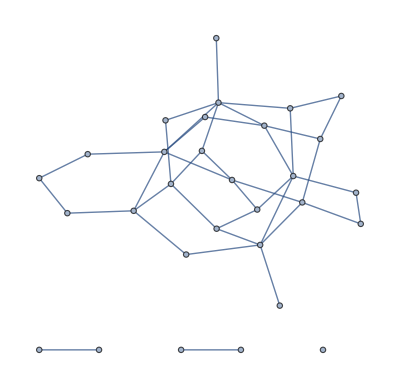
```mathematica
haha=-Graphics-;
```

```mathematica
PlanarGraphQ[haha]//AbsoluteTiming
```

{0.0000843865,False}